# Curso de Verão 2020 - Instituto de Física da USP

Prof. Dr. Alexandre Levine

DFMT - IFUSP

Minicurso “Técnicas para resolver problemas de física com Mathematica®”

Nesse minicurso vamos aprender como resolver problemas de física básica e avançada com sistema de álgebra computacional Mathematica®.

• Mecânica: oscilador harmónico, pêndulo físico

Livro texto: P. T. Tam, A Physicist’s Guide to Mathematica®. Os arquivos contem informações do livro e Wolfram Demonstration Project adotados por Marcela Babini , estudante de Mestrado IFUSP.

10 a 14 de fevereiro de 2020

## AULA 2 - OSCILADOR HARMÔNICO COM MATHEMATICA®

## Mola: Solução Analítica Geral

Para a solução do primeiro problema com Mathematica, o movimento de uma mola, vamos especificar as duas equações do movimento e resolver o sistema de equações diferenciais.

```mathematica
ClearAll["Global`*"];
eqn1=(x'[t]==v[t]);(*Equação 1: definição de velocidade instantânea*)
eqn2=(v'[t]==-Subscript[ω, 0]^2 x[t]); (*Equação 2: 2a Lei de Newton para molas*)
sys1={eqn1,eqn2}; (* Sistema juntando com {} as equações 1 e 2, para resolver analiticamente  usando o comando DSolve*)
DSolve[sys1,{x[t],v[t]},t]
```

{{v[t]→C[1] Cos[t ω_0]-C[2] Sin[t ω_0] ω_0,x[t]→C[2] Cos[t ω_0]+(C[1] Sin[t ω_0])/ω_0}}

## Mola: Solução Particular, com Duas Condições Iniciais

Agora, vamos adicionar uma condição inicial para a coordenada e outra para a velocidade inicial.

```mathematica
ClearAll["Global`*"];
eqn3=x''[t]==-Subscript[ω, 0]^2 x[t]; (*Equação 3: 2a Lei de Newton*)
eqn4=x[0]==A; (*Equação 4: 1a condição inicial, para coordenada*)
eqn5=x'[0]==Subscript[v, 0]; (*Equação 5: 2a condição inicial, para velocidade*)
sys2={eqn3,eqn4,eqn5}; (* Sistema juntando com {} as equações 3, 4 e 5, para resolver analiticamente  usando o comando DSolve*)
DSolve[sys2,x[t],t]
```

{{x[t]→(Sin[t ω_0] v_0+A Cos[t ω_0] ω_0)/ω_0}}

## Movimento em Campo Eletromagnético

Até aqui, estudamos o movimento em uma dimensão. Para o estudo de um movimento bidimensional, vamos solucionar as equações do movimento de uma partícula com massa m carga q que parte do repouso dentro de uma campo eletromagnético uniforme e, depois, faremos o gráfico com a trajetória da partícula. Partiremos das seguintes equações:

ẍ=q/m E_x+ω_c y^˙     e     ÿ=q/m E_y-ω_c x^˙,   onde   ω_c=qB/m

Condições iniciais: em    t=0,  x=y=x^˙=y^˙=0.

```mathematica
ClearAll["Global`*"];
eqn6=x''[t]==q/m Ex+Subscript[ω, C] y'[t]; (*Equações 6 e 7: 2a Lei de Newton para as forças elétrica e magnética atuando sobre a partícula*)
eqn7=y''[t]==q/m Ey-Subscript[ω, C] x'[t];
ic3={x[0]==0,x'[0]==0,y[0]==0,y'[0]==0}; (*Condições iniciais: corpo partindo do repouso e da posição (0,0) *)
sys3={eqn6,eqn7,ic3}; (*Sistema juntando com {} as equações 6 e 7, para resolver analiticamente  usando o comando DSolve*)
sol=FactorTerms[Simplify[DSolve[sys3,{x[t],y[t]},t] ]]/.{(Ex q)/(m Subscript[ω, C]^2)->a,(Ey q)/(m Subscript[ω, C]^2)->b,(Ey q)/(m Subscript[ω, C])->b Subscript[ω, C],(Ex q)/(m Subscript[ω, C])->a Subscript[ω, C]};(*ponto e vírgula impede de lançar a conta n output*)

Dsolve[sys3,{x[t],y[t]},t]
Simplify[[Dsolve[sys3,{x[t],y[t]},t]]
```

Dsolve[{x''[t]==(Ex q)/m+ω_C y'[t],y''[t]==(Ey q)/m-ω_C x'[t],{x[0]==0,x'[0]==0,y[0]==0,y'[0]==0}},{x[t],y[t]},t]

Para plotar o gráfico da trajetória da partícula, vamos achar os valores de x e y numericamente, dentro de um intervalo de tempo:

a-a Cos[t ω_C]-b Sin[t ω_C]+b t ω_C

b-b Cos[t ω_C]+a Sin[t ω_C]-a t ω_C

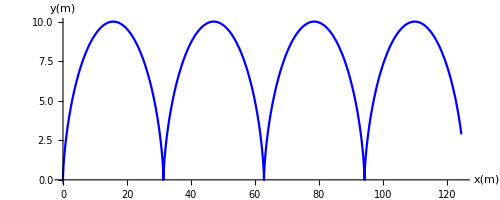

```mathematica
X[t_]=x[t]/.sol[[1,1]]
Y[t_]=y[t]/.sol[[1,2]]
ParametricPlot[{X[t],Y[t]}/.{a->0,b->5,Subscript[ω, C]->6},{t,0,4},AxesLabel->{"x(m)","y(m)"}, PlotStyle->Blue]
```

## Pêndulo: Diagrama de Fase

Vamos resolver numericamente as equações de movimento e plotar os diagramas de fase de três tipos de pêndulo: simples, amortecido e amortecido-forçado. Para isso, usaremos o comendo NDSolve.

#### Pêndulo Simples

#### -Graphics--Graphics- -Graphics- -Graphics-

#### -Graphics-, -Graphics-

#### ,

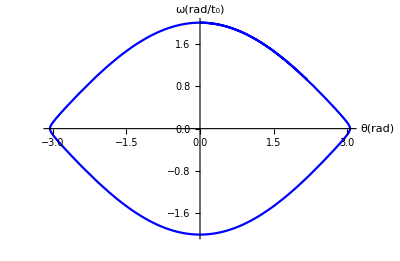

```mathematica
ClearAll["Global`*"];
Subscript[F, R][t_]=- Sin[θ[t]];
ci={θ[0]==0,ω[0]==2-0.002};
points1=NDSolve[
{θ' [t]==ω[t],
ω'[t]==Subscript[F, R][t],
ci},
 {θ,ω},{t,0,19,5}]; (*Junta eqs numa sistema para resolver Numericamente usando comando NDSolve*)

ParametricPlot[Evaluate[{θ[t],ω[t]}/.points1],
{t,0,19.4},AxesLabel->{"θ(rad)","ω(rad/t_0)"}, PlotStyle->Blue]
```

#### Pêndulo Amortecido

#### -Graphics-

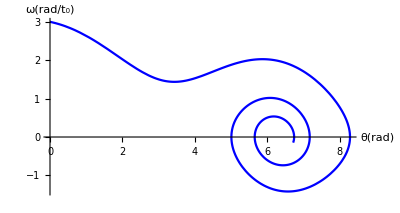

```mathematica
ClearAll["Global`*"];
Subscript[F, R2][t_]:=- Sin[θ[t]]-0.2ω[t];
ci2={θ[0]==0,ω[0]==3};
points1=NDSolve[
{θ'[t]==ω[t],
ω'[t]==Subscript[F, R2][t],
ci2},{θ,ω},{t,0,19,5}];
ParametricPlot[Evaluate[{θ[t],ω[t]}/.points1],{t,0,19.4},AxesLabel->{"θ(rad)","ω(rad/t_0)"}, PlotStyle->Blue]
```

#### Pêndulo Amortecido-forçado

#### -Graphics-

```mathematica
ClearAll["Global`*"];
{a,F,ωf}={0.2,0.52,0.694};(*lista *)
cycles=50;

Subscript[F, R3][t_]:=- Sin[θ[t]]-a ω[t] +F Cos[ωf t];
ci3={θ[0]==0.8,ω[0]==0.8};(*condições iniciais*)

sol3=NDSolve[
{θ'[t]==ω[t],ω'[t]==Subscript[F, R3][t],ci3},
{θ,ω},{t,0,cycles(2Pi/ωf)},MaxSteps->20000];
```

Matematicamente, o ângulo x pode assumir qualquer valor. Porém, fisicamente, x só pode assumir valores entre -π e π. Por isso, vamos reduzir os ângulos encontrados anteriormente usando uma função que criaremos para isso:

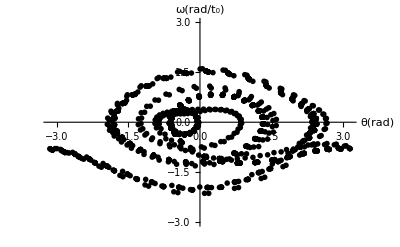

```mathematica
reduce[θ_]:=Mod[θ,2π]/;Mod[θ,2π]≤ π;
reduce[θ_]:=(Mod[θ,2π]-2π)/;Mod[θ,2π]> π
steps=30;
points3=Flatten[Table[{θ[t],ω[t]}/.sol3,{t,0,cycles(2Pi/ωf),(1/steps)(2π/ωf)}],1];
newpoints3={reduce[#[[1]]],#[[2]]}&/@points3;

ListPlot[newpoints3,PlotRange->{-3,3},AxesLabel->{"θ(rad)","ω(rad/t_0)"}]
```

#### Seção de Poincaré

A seção de Poincaré promove uma simplificação do diagrama de fase, revelando características essenciais da dinâmica analisada. Para o diagrama de fases, os pontos são calculados para os intervalos de tempo t=0, Δt, 2Δt, 3Δt, ..., onde escolhemos Δt=T/30, em que T=2π/ωf é o período da força. Para a seção de Poincaré, selecionamos somente os pontos para t=0, T, 2T, 3T, ..., e construímos a seguinte seção:

```mathematica
poincare3=Table[newpoints3[[n]],{n,1+25 steps,Length[newpoints3],steps}];
Length[newpoints3]
Length[poincare3]
```

1501

26

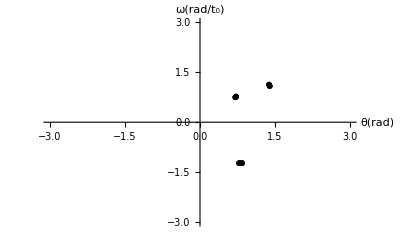

```mathematica
ListPlot[poincare3,PlotRange->{{-3,3},{-3,3}},AxesLabel->{"θ(rad)","ω(rad/t_0)"}]
```

O gráfico gerado contém três pontos, o que indica movimento periódico. Vamos fazer outro exemplo, com condições iniciais diferentes:

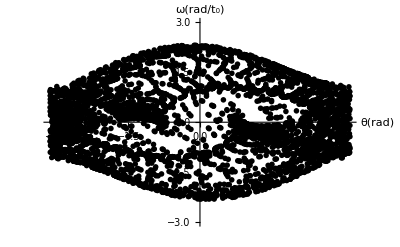

```mathematica
{a,F,ωf}={1/2,1.15,2/3};
cycles=180;

Subscript[F, R3][t_]:=- Sin[θ[t]]-a ω[t] +F Cos[ωf t];
ci3={θ[0]==0.8,ω[0]==0.8};

sol4=NDSolve[
{θ'[t]==ω[t],ω'[t]==Subscript[F, R3][t],ci3},
{θ,ω},{t,0,cycles(2Pi/ωf)},MaxSteps->200000];

steps=30;
points4=Flatten[Table[{θ[t],ω[t]}/.sol4,{t,0,cycles(2Pi/ωf),(1/steps)(2π/ωf)}],1];
newpoints4={reduce[#[[1]]],#[[2]]}&/@points4;

ListPlot[newpoints4,PlotRange->{-3,3},AxesLabel->{"θ(rad)","ω(rad/t_0)"}]
```

A nova seção de Poincaré fica:

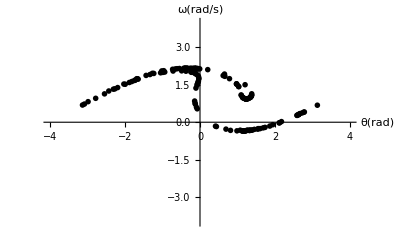

```mathematica
poincare4=Table[newpoints4[[n]],{n,1+20 steps,Length[newpoints4],steps}];
ListPlot[poincare4,PlotRange->{{-4,4},{-4,4}},AxesLabel->{"θ(rad)","ω(rad/t_0)"}]
```

O gráfico agora tem uma geometria complexa, característica de movimentos caóticos. Para finalizar, vamos criar uma animação que mostra como o movimento do pêndulo muda de acordo com determinadas condições:

```mathematica
ClearAll["Global`*"];
f[x_]:=If[x≥Pi,-Pi+(x-Pi),If[x≤-Pi,Pi+(x+Pi),x]];
Evolution2[n_,{x0_,v0_},dt_,k_,d_]:=
Module[{flow={},i=0,x=x0,v=v0,tmpx=0,tmpv=0,a=0},
For[i=1,i≤n,
AppendTo[flow,{x,v}];
tmpx=x;
tmpv=v;
a=-k Sin[x]-d v;
v+=a dt;
x+=v dt;x=f[x];
;i++];
flow];

Manipulate[
l=Evolution2[700,{0,v},0.02,1/e,d];Grid[{{Show[
ListPlot[l,PlotRange->{{-π-0.2,π+0.2},{-Abs[v]-0.3,Abs[v]+0.3}},ImageSize->{275,275},AxesLabel->{Style["θ",Bold],Style["ω",Bold]},ImagePadding->25],
Graphics[{Red,PointSize[0.03],Point[{l[[a,1]],l[[a,2]]}]}]],Graphics[{{EdgeForm[Thick],Red,Rotate[Disk[{0,0.4},{0.05,0.4}],l⟦a,1⟧+Pi,{0,0}]},{Blue,PointSize[0.02],Point[{0,0}]},{Dashed,Pink,Circle[{0,0},0.8]},{Dashed,Blue,Line[{{-1,0},{1,0}}]}},PlotRange->1,ImageSize->{275,275}]}},Frame->All],
{{a,1,"step"},1,500,1},
{{e,1,"pendulum length"},1,2.5},
{{v,2,"angular velocity"},-10,10},
{{d,0,"damping"},0,1},TrackedSymbols->Manipulate,SaveDefinitions->True]
```